```mathematica
SetDirectory["/home/kamano/gitsrc/ChemicalStructureRecognition"]
```

/home/kamano/gitsrc/ChemicalStructureRecognition

## Images

```mathematica
cdata=ChemicalData[];
```

```mathematica
ldata=Length[cdata]
```

44089

### create test

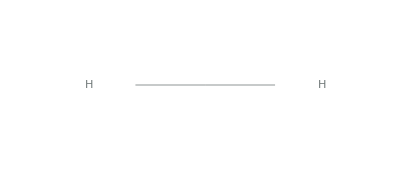

```mathematica
ChemicalData[cdata[[1]]]
```

```mathematica
r[1]=Rasterize[ChemicalData[cdata[[1]]],RasterSize->300,ImageSize->100]
```

-Graphics-

```mathematica
Information[r[1]]
```

Image

```mathematica
br[1]=Binarize[r[1]]
```

-Graphics-

```mathematica
(*Export["OSRA-test/br1.jpg",br[1]]*)
```

OSRA-test/br1.jpg

```mathematica
s=ChemicalData[cdata[[1]],"SMILES"]
```

[HH]

### random selection

```mathematica
len=50
```

50

```mathematica
rs={39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}
```

{39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}

```mathematica
(*rs=RandomSample[Range[ldata],len]*)
```

{39628,8924,5540,37508,38397,43288,30646,2945,29820,32286,28281,17023,11401,9910,15290,16933,35978,40439,15657,32027,19707,7486,13838,5810,16301,21714,7405,27756,8595,15397,24766,23711,13509,34262,28913,20008,26901,21734,37166,38012,3040,43691,13235,37832,17538,17242,1661,1989,12604,5184}

```mathematica
ims=Map[(r[#]=Rasterize[ChemicalData[cdata[[#]]],RasterSize->300,ImageSize->100])&,rs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
smiles=Map[(s[#]=ChemicalData[cdata[[#]],"SMILES"])&,rs];
```

```mathematica
Table[Export["OSRA-test/"<>ToString[rs[[n]]]<>".txt",smiles[[n]]],{n,len}]
```

{OSRA-test/39628.txt,OSRA-test/8924.txt,OSRA-test/5540.txt,OSRA-test/37508.txt,OSRA-test/38397.txt,OSRA-test/43288.txt,OSRA-test/30646.txt,OSRA-test/2945.txt,OSRA-test/29820.txt,OSRA-test/32286.txt,OSRA-test/28281.txt,OSRA-test/17023.txt,OSRA-test/11401.txt,OSRA-test/9910.txt,OSRA-test/15290.txt,OSRA-test/16933.txt,OSRA-test/35978.txt,OSRA-test/40439.txt,OSRA-test/15657.txt,OSRA-test/32027.txt,OSRA-test/19707.txt,OSRA-test/7486.txt,OSRA-test/13838.txt,OSRA-test/5810.txt,OSRA-test/16301.txt,OSRA-test/21714.txt,OSRA-test/7405.txt,OSRA-test/27756.txt,OSRA-test/8595.txt,OSRA-test/15397.txt,OSRA-test/24766.txt,OSRA-test/23711.txt,OSRA-test/13509.txt,OSRA-test/34262.txt,OSRA-test/28913.txt,OSRA-test/20008.txt,OSRA-test/26901.txt,OSRA-test/21734.txt,OSRA-test/37166.txt,OSRA-test/38012.txt,OSRA-test/3040.txt,OSRA-test/43691.txt,OSRA-test/13235.txt,OSRA-test/37832.txt,OSRA-test/17538.txt,OSRA-test/17242.txt,OSRA-test/1661.txt,OSRA-test/1989.txt,OSRA-test/12604.txt,OSRA-test/5184.txt}

```mathematica
Table[Export["OSRA-test/"<>ToString[rs[[n]]]<>".jpg",ims[[n]]],{n,len}]
```

{OSRA-test/39628.jpg,OSRA-test/8924.jpg,OSRA-test/5540.jpg,OSRA-test/37508.jpg,OSRA-test/38397.jpg,OSRA-test/43288.jpg,OSRA-test/30646.jpg,OSRA-test/2945.jpg,OSRA-test/29820.jpg,OSRA-test/32286.jpg,OSRA-test/28281.jpg,OSRA-test/17023.jpg,OSRA-test/11401.jpg,OSRA-test/9910.jpg,OSRA-test/15290.jpg,OSRA-test/16933.jpg,OSRA-test/35978.jpg,OSRA-test/40439.jpg,OSRA-test/15657.jpg,OSRA-test/32027.jpg,OSRA-test/19707.jpg,OSRA-test/7486.jpg,OSRA-test/13838.jpg,OSRA-test/5810.jpg,OSRA-test/16301.jpg,OSRA-test/21714.jpg,OSRA-test/7405.jpg,OSRA-test/27756.jpg,OSRA-test/8595.jpg,OSRA-test/15397.jpg,OSRA-test/24766.jpg,OSRA-test/23711.jpg,OSRA-test/13509.jpg,OSRA-test/34262.jpg,OSRA-test/28913.jpg,OSRA-test/20008.jpg,OSRA-test/26901.jpg,OSRA-test/21734.jpg,OSRA-test/37166.jpg,OSRA-test/38012.jpg,OSRA-test/3040.jpg,OSRA-test/43691.jpg,OSRA-test/13235.jpg,OSRA-test/37832.jpg,OSRA-test/17538.jpg,OSRA-test/17242.jpg,OSRA-test/1661.jpg,OSRA-test/1989.jpg,OSRA-test/12604.jpg,OSRA-test/5184.jpg}

```mathematica
Table[Export["OSRA-test/"<>ToString[rs[[n]]]<>".png",ims[[n]]],{n,len}]
```

{OSRA-test/39628.png,OSRA-test/8924.png,OSRA-test/5540.png,OSRA-test/37508.png,OSRA-test/38397.png,OSRA-test/43288.png,OSRA-test/30646.png,OSRA-test/2945.png,OSRA-test/29820.png,OSRA-test/32286.png,OSRA-test/28281.png,OSRA-test/17023.png,OSRA-test/11401.png,OSRA-test/9910.png,OSRA-test/15290.png,OSRA-test/16933.png,OSRA-test/35978.png,OSRA-test/40439.png,OSRA-test/15657.png,OSRA-test/32027.png,OSRA-test/19707.png,OSRA-test/7486.png,OSRA-test/13838.png,OSRA-test/5810.png,OSRA-test/16301.png,OSRA-test/21714.png,OSRA-test/7405.png,OSRA-test/27756.png,OSRA-test/8595.png,OSRA-test/15397.png,OSRA-test/24766.png,OSRA-test/23711.png,OSRA-test/13509.png,OSRA-test/34262.png,OSRA-test/28913.png,OSRA-test/20008.png,OSRA-test/26901.png,OSRA-test/21734.png,OSRA-test/37166.png,OSRA-test/38012.png,OSRA-test/3040.png,OSRA-test/43691.png,OSRA-test/13235.png,OSRA-test/37832.png,OSRA-test/17538.png,OSRA-test/17242.png,OSRA-test/1661.png,OSRA-test/1989.png,OSRA-test/12604.png,OSRA-test/5184.png}

### train test

```mathematica
NetTrain[{1->s,1->s}]
```

NetTrain[{1→[HH],1→[HH]}]